```mathematica
SusceptHeight={{4,1.310617,0.00520}, {8, 4.002690545,0.029074},{16,12.953, 0.1056}, {32, 41.5689916, 1.2237}};
SusceptHeightPoints = Table[Log[{SusceptHeight[[i]][[1]],SusceptHeight[[i]][[2]]}], {i, 1, Length[SusceptHeight]}];
SusceptHeightErrors = Table[SusceptHeight[[i]][[3]]/SusceptHeight[[i]][[2]],{i,1,Length[SusceptHeight]}];
SusceptWidth={{4, 0.0541,0.00049}, {8,0.026319, 0.000420}, {16,0.01256, 0.000278},{32, 0.006609, 0.000726}};
SusceptWidthPoints = Table[Log[{SusceptWidth[[i]][[1]],SusceptWidth[[i]][[2]]}], {i, 1, Length[SusceptWidth]}];
SusceptWidthErrors = Table[SusceptWidth[[i]][[3]]/SusceptWidth[[i]][[2]],{i,1,Length[SusceptWidth]}];
SusceptPos={{4, 0.14014395,0.00029}, {8, 0.166519, 0.000259}, {16,0.1786131974,0.00017583},{32, 0.18383, 0.0003149}};
SusceptPosPoints = Table[{SusceptPos[[i]][[1]],SusceptPos[[i]][[2]]}, {i, 1, Length[SusceptPos]}];
SusceptPosErrors = Table[SusceptPos[[i]][[3]],{i,1,Length[SusceptPos]}];
Needs["ErrorBarPlots`"]
```

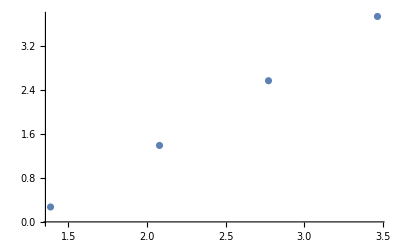

```mathematica
ListPlot[SusceptHeightPoints]
```

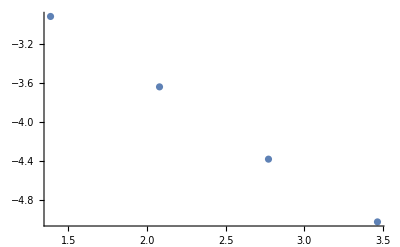

```mathematica
ListPlot[SusceptWidthPoints]
```

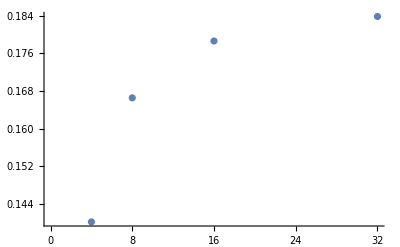

```mathematica
ListPlot[SusceptPosPoints]
```

```mathematica
SusceptHeightFit = NonlinearModelFit[SusceptHeightPoints,(sigmav) x + b, {{sigmav,0.5}, {b,0.5}},x,Weights->1/SusceptHeightErrors^2];
```

```mathematica
SusceptHeightFit[{"BestFit","ParameterTable"}]
```

{-2.01751+1.64785 x, | Estimate | Standard Error | t-Statistic | P-Value
sigmav | 1.64785 | 0.0147892 | 111.423 | 0.0000805381
b | -2.01751 | 0.0271907 | -74.1985 | 0.00018159}

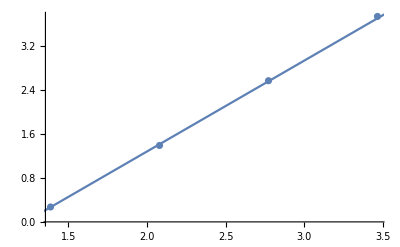

```mathematica
Show[
ErrorListPlot[
Table[{SusceptHeightPoints[[i]][[1]],SusceptHeightPoints[[i]][[2]], SusceptHeightErrors[[i]]},{i,1,Length[SusceptHeightPoints]}]],
Plot[SusceptHeightFit[x],{x,0,5},PlotRange->Full]
]
```

```mathematica
SusceptWidthFit = NonlinearModelFit[SusceptWidthPoints,-(1/v) x + b, {v, b},x,Weights->1/SusceptWidthErrors^2];
```

```mathematica
SusceptWidthFit[{"BestFit","ParameterTable"}]
```

{-1.46472-1.04717 x, | Estimate | Standard Error | t-Statistic | P-Value
v | 0.954953 | 0.0083054 | 114.98 | 0.0000756324
b | -1.46472 | 0.0161126 | -90.9048 | 0.00012099}

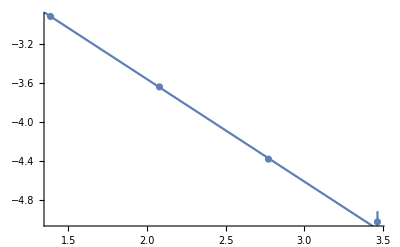

```mathematica
Show[
ErrorListPlot[Table[{SusceptWidthPoints[[i]][[1]],SusceptWidthPoints[[i]][[2]], SusceptWidthErrors[[i]]},{i,1,Length[SusceptWidthPoints]}]],
Plot[SusceptWidthFit[x],{x,0,5},PlotRange->Full]
]
```

```mathematica
SusceptPosFit = NonlinearModelFit[SusceptPosPoints, A*x^(-v) + b, {A,v, b},x,Weights->1/SusceptPosErrors^2];
```

```mathematica
SusceptPosFit[{"BestFit","ParameterTable"}]
```

{0.188373-0.23694/x^1.14799, | Estimate | Standard Error | t-Statistic | P-Value
A | -0.23694 | 0.00575104 | -41.1996 | 0.0154491
v | 1.14799 | 0.0214191 | 53.5967 | 0.0118766
b | 0.188373 | 0.000361186 | 521.539 | 0.00122065}

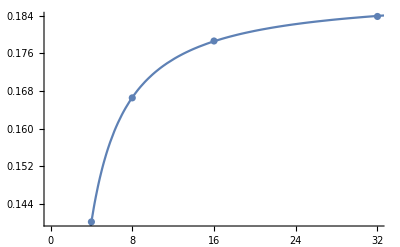

```mathematica
Show[
ErrorListPlot[Table[{SusceptPosPoints[[i]][[1]],SusceptPosPoints[[i]][[2]], SusceptPosErrors[[i]]},{i,1,Length[SusceptPosPoints]}]],
Plot[SusceptPosFit[x],{x,0.1,150},PlotRange->Full]
]
```

```mathematica
MagnetizationHeight = {{8, 0.90404375}, {16,0.841697265625}, {32,0.774832519531}, {64,0.711084960937}, {128, 0.659222839355}};
```

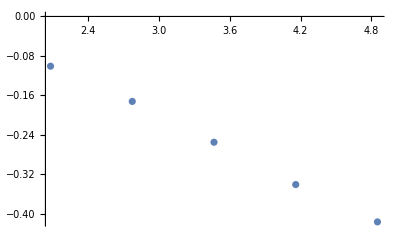

```mathematica
ListPlot[Log[MagnetizationHeight]]
```

```mathematica
MagnetizationHeightFit = NonlinearModelFit[Log[MagnetizationHeight],-(betav) x + b, {betav, b},x];
```

```mathematica
MagnetizationHeightFit[{"BestFit","ParameterTable"}]
```

{0.142935-0.115453 x, | Estimate | Standard Error | t-Statistic | P-Value
betav | 0.115453 | 0.00197076 | 58.5831 | 0.0000109572
b | 0.142935 | 0.00709809 | 20.1371 | 0.000267694}

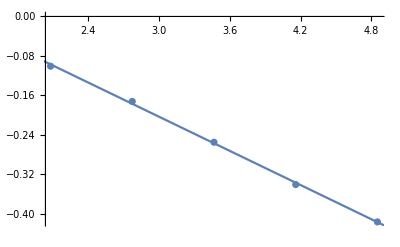

```mathematica
Show[ListPlot[Log[MagnetizationHeight]],Plot[MagnetizationHeightFit[x],{x,0,5}]]
```